```mathematica
SetDirectory["D:\\study\\西安理工大学\\thesis\\论文\\nb"];
```

```mathematica
Clear["@"];
(*dd=Reap[For[i=50,i≤81,i++,
id=Import["ca_"<>ToString[i]<>".txt","Data"];
If[i==55||i==59,,Sow[id]];]];
*)
dd=Reap[
For[i=51,i≤81,i++,
Sow[Import["ca_"<>ToString[i]<>".txt","Table"]];
]];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<BISfit`
```

```mathematica
data=dd[[2,1]];

fdata=Map[Filterd,data];
(*fdata[[All,All,1]]*)
(*ListPlot[fdata[[All,All,2]]]*)
ss=Table[Length[fdata[[i]]],{i,Length[fdata]}];
```

```mathematica
fd=fdata;
Reap[For[i=1,i≤Length[ss],i++,
If[ss[[i]]≥7,,Sow[i+50]]
]]
(*tt=Table[Length[fd[[i]]],{i,Length[fd]}]*)
Length[fd]
```

{Null,{{55,59,61,62,66,74,76}}}

31

```mathematica
(*translate data to complex numbers*)
SetDirectory["E:\\work\\thesis\\论文\\codes\\data\\"];
ff=FileNames["C*.dat"];
dd=Reap[For[i=1,i≤Length[ff],i++,
Sow[Import[ff[[i]],"Table"]];
]];
data=dd[[2,1]];
```

```mathematica
Dimensions[data]
```

{25,32,16}

```mathematica
data[[1]];
(*partition into list of nX2*)
transdt=Reap[
For[i=1,i<Length[data],i++,
For[j=1,j<Length[data[[i,1]]]/2,j++,
dxy=data[[i]][[All,{2j-1,2j}]];
X=Map[Function[x,x[[1]]Cos[-x[[2]]π/(180)]],dxy];
	   Y=Map[Function[x,x[[1]]Sin[-x[[2]]π/(180)]],dxy];
Sow[Table[{X[[t]]+ⅈ Y[[t]]},{t,Length[X]}]];
]]
][[2,1]];
```

```mathematica
Dimensions[transdt]
```

{168,32,1}

```mathematica
For[i=1,i<=Length[data],i++,
transdt=Reap[
For[j=1,j<=Length[data[[i,1]]]/2,j++,
dxy=data[[i]][[All,{2j-1,2j}]];
Sow[Table[Map[Function[x,x[[1]]Cos[-x[[2]]π/(180)]],dxy][[t]]+ⅈ Map[Function[x,x[[1]]Sin[-x[[2]]π/(180)]],dxy][[t]],{t,Length[dxy]}]];
]
][[2,1]];

Export["complex_"<>ToString[i]<>".mat",transdt,"Mat"];

];
```

{8,32}

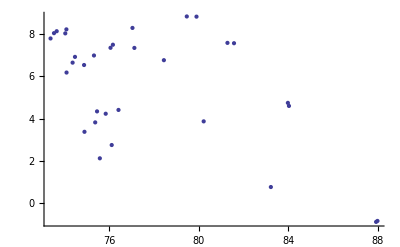

```mathematica
out=(*Partition[*)Flatten[Z];
ListPlot[Transpose[{Re[out[[1;;32]]],Im[out[[1;;32]]]}]]
```

```mathematica
Export["rc00.dat",out,"Data"]
```

rc00.dat